```mathematica
rawLow={{14521,145.43},{15127,145.21},{15867,134.41},{18401,121.29},{19969,114.24},{22473,107.88},{24368,103.73},{25690,94.62},{29510,86.7},{30766,75.07},{32504,73.26},{34345,67.35}};
low={{14521,145.43},{14719.2,145.699},{14917.5,145.988},{15115.7,145.299},{15314,142.893},{15512.2,139.455},{15710.4,136.153},{15908.7,134.108},{16106.9,132.744},{16305.2,131.487},{16503.4,130.324},{16701.6,129.242},{16899.9,128.226},{17098.1,127.263},{17296.4,126.34},{17494.6,125.442},{17692.8,124.557},{17891.1,123.671},{18089.3,122.77},{18287.6,121.84},{18485.8,120.872},{18684,119.887},{18882.3,118.906},{19080.5,117.942},{19278.8,117.012},{19477,116.129},{19675.2,115.309},{19873.5,114.566},{20071.7,113.907},{20270,113.295},{20468.2,112.719},{20666.4,112.174},{20864.7,111.656},{21062.9,111.16},{21261.2,110.681},{21459.4,110.216},{21657.6,109.76},{21855.9,109.308},{22054.1,108.856},{22252.4,108.399},{22450.6,107.933},{22648.8,107.495},{22847.1,107.127},{23045.3,106.804},{23243.6,106.498},{23441.8,106.18},{23640,105.823},{23838.3,105.4},{24036.5,104.882},{24234.8,104.243},{24433,103.434},{24631.2,102.233},{24829.5,100.716},{25027.7,99.052},{25226,97.4109},{25424.2,95.9626},{25622.4,94.8769},{25820.7,94.2058},{26018.9,93.6438},{26217.2,93.1534},{26415.4,92.7248},{26613.6,92.3484},{26811.9,92.0146},{27010.1,91.7136},{27208.4,91.4358},{27406.6,91.1716},{27604.8,90.9112},{27803.1,90.6451},{28001.3,90.3635},{28199.6,90.0568},{28397.8,89.7153},{28596,89.3294},{28794.3,88.8894},{28992.5,88.3856},{29190.8,87.8083},{29389,87.148},{29587.2,86.3314},{29785.5,84.8321},{29983.7,82.7765},{30182,80.4662},{30380.2,78.2029},{30578.4,76.2881},{30776.7,75.0226},{30974.9,74.3196},{31173.2,73.9044},{31371.4,73.7065},{31569.6,73.6552},{31767.9,73.6799},{31966.1,73.71},{32164.4,73.6749},{32362.6,73.5039},{32560.8,73.1338},{32759.1,72.6405},{32957.3,72.076},{33155.6,71.4548},{33353.8,70.7914},{33552,70.1003},{33750.3,69.3962},{33948.5,68.6933},{34146.8,68.0065}};rawHigh={{14951,158.68},{16072,159.49},{17812,157.13},{19411,140.48},{21993,135.59},{24934,125.93},{25992,121.31},{28134,102.97},{31395,100.41},{33821,96.37},{34490,88.96},{35438,86.35}};
high={{14951,158.68},{15155.9,158.867},{15360.7,159.096},{15565.6,159.317},{15770.5,159.476},{15975.4,159.522},{16180.2,159.448},{16385.1,159.437},{16590,159.465},{16794.8,159.472},{16999.7,159.398},{17204.6,159.182},{17409.4,158.766},{17614.3,158.088},{17819.2,157.089},{18024,155.547},{18228.9,153.441},{18433.8,150.974},{18638.7,148.346},{18843.5,145.76},{19048.4,143.415},{19253.3,141.514},{19458.1,140.243},{19663,139.351},{19867.9,138.656},{20072.7,138.128},{20277.6,137.736},{20482.5,137.449},{20687.4,137.236},{20892.2,137.066},{21097.1,136.908},{21302,136.732},{21506.8,136.506},{21711.7,136.199},{21916.6,135.781},{22121.4,135.246},{22326.3,134.675},{22531.2,134.079},{22736.1,133.459},{22940.9,132.819},{23145.8,132.159},{23350.7,131.483},{23555.5,130.792},{23760.4,130.089},{23965.3,129.376},{24170.1,128.654},{24375,127.927},{24579.9,127.196},{24784.8,126.463},{24989.6,125.735},{25194.5,125.046},{25399.4,124.336},{25604.2,123.512},{25809.1,122.481},{26014,121.151},{26218.8,119.518},{26423.7,117.669},{26628.6,115.671},{26833.5,113.594},{27038.3,111.504},{27243.2,109.471},{27448.1,107.562},{27652.9,105.847},{27857.8,104.394},{28062.7,103.271},{28267.5,102.488},{28472.4,101.878},{28677.3,101.408},{28882.2,101.063},{29087,100.824},{29291.9,100.676},{29496.8,100.601},{29701.6,100.583},{29906.5,100.605},{30111.4,100.65},{30316.2,100.702},{30521.1,100.743},{30726,100.758},{30930.9,100.728},{31135.7,100.638},{31340.6,100.47},{31545.5,100.244},{31750.3,100.039},{31955.2,99.8467},{32160.1,99.653},{32364.9,99.4446},{32569.8,99.2082},{32774.7,98.9303},{32979.6,98.5977},{33184.4,98.1968},{33389.3,97.7142},{33594.2,97.1366},{33799,96.4505},{34003.9,94.8791},{34208.8,92.1193},{34413.6,89.5702},{34618.5,88.2755},{34823.4,87.5596},{35028.3,87.1318},{35233.1,86.7945},{35438,86.35}};
```

```mathematica
Needs["PlotLegends`"]
```

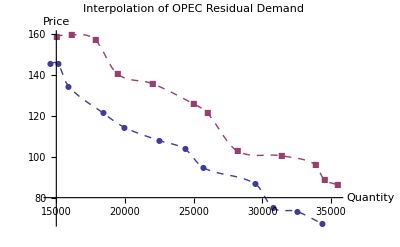

```mathematica
Show[ListPlot[{low,high},PlotRange->Full,Joined->True,PlotStyle->Dashed],
ListPlot[{rawLow,rawHigh},PlotMarkers->{Automatic,8}],
AxesLabel->{"Quantity","Price"},PlotLabel->"Interpolation of OPEC Residual Demand"]
```